```mathematica
Remove["Global`*"];
```

```mathematica
coord = {t,r,θ,ϕ};
(*J is angular momentum of black hole. J->0 means the metric becomes Schwartzchild.*)
G=1;M=1;J=10;
```

```mathematica
rs=2 G M;α=J/M;ρ=√(r^2+α^2 Cos[θ]^2);Δ=r^2-rs r+α^2;
metric= ({{(rs r)/ρ^2-1, 0, 0, -(2 rs r α Sin[θ]^2)/ρ^2}, {0, ρ^2/Δ, 0, 0}, {0, 0, ρ^2, 0}, {-(2 rs r α Sin[θ]^2)/ρ^2, 0, 0, Sin[θ]^2(r^2+α^2+(rs r α^2)/ρ^2 Sin[θ]^2)}});
inversemetric = Inverse[metric];
```

```mathematica
affine= Simplify[Table[1/2 Sum[inversemetric[[i, m]] (D[metric[[m, k]], coord[[j]]] + D[metric[[m, j]], coord[[k]]] - D[metric[[j, k]], coord[[m]]]),{m, 1, 4}], {i, 1, 4}, {j, 1, 4}, {k, 1, 4}]];
affine=affine/.{t->t[τ],r->r[τ],θ->θ[τ],ϕ->ϕ[τ]};

(*pretty print Christoffel symbols*)
listaffine:=Table[If[UnsameQ[affine[[i,j,k]],0],{ToString[Γ[i,j,k]],affine[[i,j,k]]}] ,{i,1,4},{j,1,4},{k,1,j}]
TableForm[Partition[DeleteCases[Flatten[listaffine],Null],2],TableSpacing->{2,2}];
```

```mathematica
geod = Table[coord[[i]]''[τ] ==- Sum[affine[[i, j, k]] coord[[j]]'[τ] coord[[k]]'[τ], {j, 1, 4}, {k, 1, 4}],{i, 1, 4}]//Simplify;
```

```mathematica
(*Flatten[Table[Solve[geod[[i]],coord[[i]]''[τ]],{i,1,4}]]*)
```

```mathematica
r0=50;θ0=π/2;ϕ0=π/2;
dr0=0;dθ0=0;dϕ0=0;
u={dt0,dr0,dθ0,dϕ0};
(* We use u^μ Subscript[u, ν]=-1 to solve for t'[0]*)
initCond={
t[0]==0,t'[0]==Abs[dt0]/.(Flatten[Solve[Sum[metric[[μ,ν]] u[[μ]] u[[ν]],{μ,1,4}, {ν,1,4}]==-1,dt0]])/.{r->r0,θ->θ0,ϕ->ϕ0},
r[0]==r0,r'[0]==dr0,
θ[0]==θ0,θ'[0]==dθ0,
ϕ[0]==ϕ0,ϕ'[0]==dϕ0
};
```

```mathematica
tmax=10000;
soln=NDSolveValue[Join[geod,initCond], coord, {τ, 0, tmax}];
```

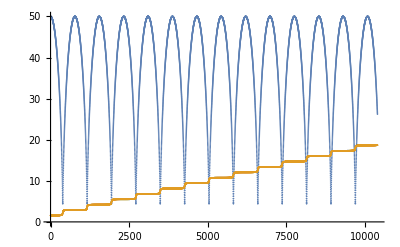

```mathematica
reh1=1/2(rs+√(rs^2-4 α^2));reh2=1/2(rs-√(rs^2-4 α^2));
radTrajRel= Table[{soln[[1]][i], soln[[2]][i]}, {i, 0,tmax}];
phiTrajRel= Table[{soln[[1]][i], soln[[4]][i]}, {i, 0,tmax}];
ListPlot[{radTrajRel,phiTrajRel},PlotRange->All,PlotLegends->"Expressions"]
```

```mathematica
x[τ_]:=soln[[2]][τ]Sin[soln[[3]][τ]]Cos[soln[[4]][τ]];
y[τ_]:=soln[[2]][τ]Sin[soln[[3]][τ]]Sin[soln[[4]][τ]];
z[τ_]:=soln[[2]][τ]Cos[soln[[3]][τ]];
a=r0;
Animate[
Graphics[{PointSize[Large],
(*Black,Point[{0, 0}],*)
Red,Point[{x[τ],y[τ]}],
Blue,Circle[{0, 0},rs],
Orange,Circle[{0, 0},reh1],
Green,Circle[{0, 0},reh2]
},PlotRange->{{-a-1,a+1},{-a-1,a+1}}],
{τ,0,tmax},AnimationRate->1000
]
```